# Symmetry adapted basis for any point group

```mathematica
Needs["GroupTheory`"];(* GTPack has to be inside your addons folder in Mathematica. https://gtpack.org/ *)
reload[p_]:=With[{pack=p},BeginPackage[pack];EndPackage[]]
Map[reload,$ContextPath];(* This command allows for autocomplete inside the GTPack package *)
```

CreateDirectory::badfile: The specified argument GroupTheory`Auxiliary`Private`dest$19398 should be a valid string or File.

CreateDirectory::ioarg: I/O operation is not valid for GroupTheory`Auxiliary`Private`dest$19398.

To illustrate this method I will use a representation of point group C3v. For simplicity I will look at the tensor square of the defining representation of O(3) on the elements of C3v. This is a 9x9 matrix representation.

```mathematica
G=GTInstallGroup[C3v];
representation=KroneckerProduct[GTGetMatrix@#,GTGetMatrix@#]&/@G; (* This is one example representation. It is a tensor square of the defining representation of O(3) *)
Grid[{G,MatrixForm/@representation},Frame->All]
```

The standard representation has changed to O(3)

Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1/4 | (√3)/4 | 0 | (√3)/4 | 3/4 | 0 | 0 | 0 | 0
-(√3)/4 | 1/4 | 0 | -3/4 | (√3)/4 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | -(√3)/2 | 0 | 0 | 0
-(√3)/4 | -3/4 | 0 | 1/4 | (√3)/4 | 0 | 0 | 0 | 0
3/4 | -(√3)/4 | 0 | -(√3)/4 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | (√3)/2 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1/4 | -(√3)/4 | 0 | -(√3)/4 | 3/4 | 0 | 0 | 0 | 0
(√3)/4 | 1/4 | 0 | -3/4 | -(√3)/4 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0
(√3)/4 | -3/4 | 0 | 1/4 | -(√3)/4 | 0 | 0 | 0 | 0
3/4 | (√3)/4 | 0 | (√3)/4 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | -(√3)/2 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | -1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1/4 | (√3)/4 | 0 | (√3)/4 | 3/4 | 0 | 0 | 0 | 0
(√3)/4 | -1/4 | 0 | 3/4 | -(√3)/4 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | -(√3)/2 | 0 | 0 | 0
(√3)/4 | 3/4 | 0 | -1/4 | -(√3)/4 | 0 | 0 | 0 | 0
3/4 | -(√3)/4 | 0 | -(√3)/4 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | -(√3)/2 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -(√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(√3)/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1/4 | -(√3)/4 | 0 | -(√3)/4 | 3/4 | 0 | 0 | 0 | 0
-(√3)/4 | -1/4 | 0 | 3/4 | (√3)/4 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0
-(√3)/4 | 3/4 | 0 | -1/4 | (√3)/4 | 0 | 0 | 0 | 0
3/4 | (√3)/4 | 0 | (√3)/4 | 1/4 | 0 | 0 | 0 | 0
0 | 0 | (√3)/2 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | (√3)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Variables needed  for the group projection operator technique

```mathematica
groupData=GTGetIreps[G,GOIrepNotation->"Mulliken"]
irreps=groupData[[2]][[2]]; (* Tables of irreps *)
irepCh=FullSimplify@(Tr/@#)&/@irreps; (* Lists of characters of irreps *)
irepNm=groupData[[1]][[3]]; (* Names of irreps *)
nirreps=GTNumberOfIreps[G]; (* Number of irreps *)
irepSize=(Length@irreps[[#,1]])&/@Range@nirreps; (* Dimensions of irreps *)
```

Representation matrices:

| Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
A_1 | (1) | (1) | (1) | (1) | (1) | (1)
A_2 | (1) | (1) | (1) | (-1) | (-1) | (-1)
E | (1 | 0
0 | 1) | (-(-1)^(1/3) | 0
0 | (-1)^(2/3)) | ((-1)^(2/3) | 0
0 | -(-1)^(1/3)) | (0 | -(-1)^(1/3)
(-1)^(2/3) | 0) | (0 | 1
1 | 0) | (0 | (-1)^(2/3)
-(-1)^(1/3) | 0)

Classes:

C_1 = {Ee}

C_2 = {(C^)_(3z)^-1,(C^)_(3z)^}

C_3 = {(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}

Character Table:

| Ee | 2 (C^)_(3z)^-1 | 3 (IC^)_(2D)^
A_1 | 1 | 1 | 1
A_2 | 1 | 1 | -1
E | 2 | -1 | 0

{{{{Ee},{(C^)_(3z)^-1,(C^)_(3z)^},{(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^}},{{1,1,1},{1,1,-1},{2,-1,0}},{A_1,A_2,E}},{{Ee,(C^)_(3z)^-1,(C^)_(3z)^,(IC^)_(2D)^,(IC^)_(2C)^,(IC^)_(2y)^},{{{{1}},{{1}},{{1}},{{1}},{{1}},{{1}}},{{{1}},{{1}},{{1}},{{-1}},{{-1}},{{-1}}},{{{1,0},{0,1}},{{-(-1)^(1/3),0},{0,(-1)^(2/3)}},{{(-1)^(2/3),0},{0,-(-1)^(1/3)}},{{0,-(-1)^(1/3)},{(-1)^(2/3),0}},{{0,1},{1,0}},{{0,(-1)^(2/3)},{-(-1)^(1/3),0}}}}}}

The given group has 3 non-equivalent irreducible representations.

The core piece of the Group Projection Operators technique

```mathematica
decompose[repchars_]:=FullSimplify@(FullSimplify@(1/(Length@G)Conjugate@irepCh).repchars); (* Returns a list of irreps' frequencies that appear in the decomposition of the representation with characters repchars_ *)
decomposeUserFriendly[repchars_]:=ToString[StringReplace[ToString[decompose[repchars].irepNm,FormatType->StandardForm],{"+"->"⊕"}],FormatType->StandardForm]; (* same thing but user/reader friendly *)
GroupProjectionOperator[μ_,representation_]:=irepSize[[μ]]/(Length@G)(Conjugate@irepCh[[μ]]).representation; (* Returns a group projection operator onto the whole irreducible subspace transforming according to irrep μ *)
(* Grupni projektor na ukupni potprostor čiji se vektori transformišu po iri μ, korisno je ali ne daje stvari u skladu sa metodom grupnih projektora od Džambe i svi vektori iz SAB za datu iru se pomešaju. *)

GroupProjectionOperatorDetailed[μ_,representation_]:=FullSimplify[irepSize[[μ]]/(Length@G)Partition[Sum[KroneckerProduct[irreps[[μ,k,1]],representation[[k]]],{k,Length@G}],Length@representation[[1]]]];(* Returns a list of group projection operators {Subscript[(P^(μ)), 11],Subscript[(P^(μ)), 12],...,(P^(μ))_(1|μ|),} The first matrix is a projector while others are push matrice which should act onto the Image of the first projector to get other symmetry adapted vectors. *)
ShomyProjection[μ_,representation_]:=Module[{out},out=irepSize[[μ]]/(Length@G)Partition[FullSimplify@Sum[KroneckerProduct[irreps[[μ,k,1]],representation[[k]]],{k,Length@G}],Length@representation[[1]]];
FullSimplify@((ConjugateTranspose[#].out[[1]].#)&/@out)](* Returns a list of projectors {Subscript[(P^(μ)), 11],Subscript[(P^(μ)), 22],Subscript[(P^(μ)), 33],...,(P^(μ))_(|µ||μ|)} *)
```

Example: the tensor square of the definitional representation of O(3) is reduced into irreps of the group C3v.

```mathematica
frequencies=decompose[Tr/@representation]
irepNm
decomposeUserFriendly[Tr/@representation]
presentIrreps=Table[If[frequencies[[i]]≠0,i,Nothing],{i,nirreps}]
```

{2,1,3}

{A_1,A_2,E}

3 E⊕2 A_1⊕A_2

{1,2,3}

A function that reduces a matrix operator_ onto one of its invariant subspaces spanned by vectors in the list basis_. If this cannot be done then you will see something not making sense.

```mathematica
operatorReduce[operator_,basis_]:=Module[{image=(operator.#)&/@basis,out={}},Transpose@Table[Flatten[Table[a[j],{j,Length@basis}]/.Solve[
Sum[a[k]basis[[k]],{k,Length@basis}]==image[[i]],Table[a[k],{k,1,Length@basis}]
],2],
{i,Length@basis}]];
DirectSum[a_List?MatrixQ,b_List?MatrixQ]:=ArrayFlatten[{{a,0},{0,b}}](* Direct sum of matrices a and b *)
```

Group Projection Operators technique. Caution, the symmetry adapted basis vectors are not normalized here. The symmetry adapted basis vectors are calculated.

```mathematica
projs=ShomyProjection[#,representation]&/@presentIrreps;(* This function returns a list of projectors Subscript[(P^(μ)), m m] . Their Image spanning vectors are then searched for. These vectors consist the symmetry adapted basis *)
SAB=Map[RowReduce,projs,{2}];
SAB=Map[(If[#==0*#,Nothing,#])&,SAB,3];
(MatrixForm/@#)&/@SAB
decomposeUserFriendly[Tr/@representation]
```

{{(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)},{(0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0)},{(1 | -ⅈ | 0 | -ⅈ | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | ⅈ | 0),(1 | ⅈ | 0 | ⅈ | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -ⅈ | 0)}}

3 E⊕2 A_1⊕A_2

Symmetry adapted basis is organized as follows

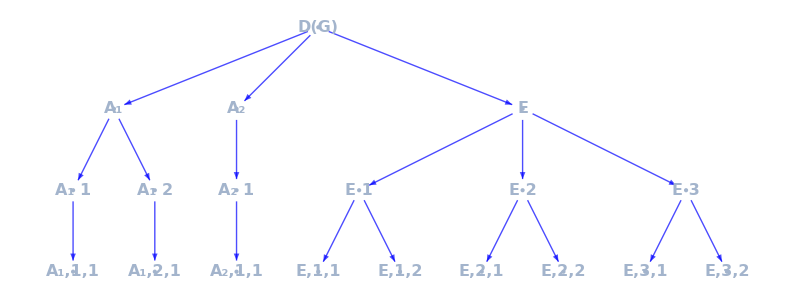

{{A_1,1,1
A_1,2,1},{A_2,1,1},{E,1,1
E,2,1
E,3,1,E,1,2
E,2,2
E,3,2}}

{{(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)},{(0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0)},{(1 | -ⅈ | 0 | -ⅈ | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | ⅈ | 0),(1 | ⅈ | 0 | ⅈ | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -ⅈ | 0)}}

```mathematica
graph=Flatten@Table[{"D(G)"->irepNm[[μ]],Table[{irepNm[[μ]]->ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t,Table[ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t->irepNm[[μ]],t,m,{m,1,irepSize[[μ]]}]},{t,1,frequencies[[μ]]}]},{μ,presentIrreps}];
ef1[el_,___]:={Arrowheads[0.01],Arrow[el,0.09]};
LayeredGraphPlot[graph,GraphLayout->"LayeredEmbedding",VertexLabels->Table[v->Placed[Style[v,Bold,16],Center],{v,VertexList@graph}],VertexShapeFunction->None,ImageSize->800,EdgeStyle->Blue,EdgeShapeFunction->ef1,PlotRangePadding->Scaled[.1]]

(MatrixForm/@#)&/@Table[Table[Column@Table[irepNm[[μ]],t,m,{t,1,frequencies[[μ]]}],{m,1,irepSize[[μ]]}],{μ,presentIrreps}]
(MatrixForm/@#)&/@SAB
```

We can check that, indeed, every matrix that represents G can be reduced in the vector space spanned by vectors μ, t_μ, m, m = 1, ..., |μ|. |μ|is the dimension of μ irrep. For instance:

```mathematica
Module[{rearrangedSAB, rearragedIrreps},
RearrangedIrreps = (MatrixForm/@#)&/@Flatten@Table[Table[ToString[irepNm[[μ]],StandardForm],{t,1,frequencies[[μ]]}],{μ,presentIrreps}];
RearrangedSAB=Table[SAB[[μ,All,t]],{μ,1,Length@presentIrreps},{t,1,frequencies[[presentIrreps[[μ]]]]}];
Grid[Join[{Prepend[G,"g ϵ G"]},Prepend[Table[(ToString[MatrixForm@operatorReduce[representation[[#]],basis],StandardForm])&/@Range@Length@G,{basis,Flatten[RearrangedSAB,1]}][[#]],RearrangedIrreps[[#]]]&/@Range@Length@RearrangedIrreps],Frame->All]]
```

g ϵ G | Ee | (C^)_(3z)^-1 | (C^)_(3z)^ | (IC^)_(2D)^ | (IC^)_(2C)^ | (IC^)_(2y)^
A_1 | (1) | (1) | (1) | (1) | (1) | (1)
A_1 | (1) | (1) | (1) | (1) | (1) | (1)
A_2 | (1) | (1) | (1) | (-1) | (-1) | (-1)
E | (1 | 0
0 | 1) | (1/2 (-1-ⅈ √3) | 0
0 | 1/2 (-1+ⅈ √3)) | (1/2 (-1+ⅈ √3) | 0
0 | 1/2 (-1-ⅈ √3)) | (0 | 1/2 (-1+ⅈ √3)
1/2 (-1-ⅈ √3) | 0) | (0 | 1/2 (-1-ⅈ √3)
1/2 (-1+ⅈ √3) | 0) | (0 | 1
1 | 0)
E | (1 | 0
0 | 1) | (1/2 (-1-ⅈ √3) | 0
0 | 1/2 (-1+ⅈ √3)) | (1/2 (-1+ⅈ √3) | 0
0 | 1/2 (-1-ⅈ √3)) | (0 | 1/2 (-1+ⅈ √3)
1/2 (-1-ⅈ √3) | 0) | (0 | 1/2 (-1-ⅈ √3)
1/2 (-1+ⅈ √3) | 0) | (0 | 1
1 | 0)
E | (1 | 0
0 | 1) | (1/2 (-1-ⅈ √3) | 0
0 | 1/2 (-1+ⅈ √3)) | (1/2 (-1+ⅈ √3) | 0
0 | 1/2 (-1-ⅈ √3)) | (0 | 1/2 (-1+ⅈ √3)
1/2 (-1-ⅈ √3) | 0) | (0 | 1/2 (-1-ⅈ √3)
1/2 (-1+ⅈ √3) | 0) | (0 | 1
1 | 0)

# Water molecular orbitals

Here, molecular orbitals will be constructed from 5 atomic orbitals. These orbitals are the s orbitals on every hydrogen atom and all three p orbitals on the oxygen atom. s orbitals are invariant under rotation and therefore only transform according to the permutation representation of G. The three p orbitals do not change which atoms they belong to and therefore only transform under the l = 1 irrep of O(3). Because I want to use p_x, p_y and p_z orbitals and not spherical harmonics, this is the same as the definitional representation of O(3).

```mathematica
Clear[H]
G=GTInstallGroup[C2v]; (* Water has the symmetry group C2v *)
atoms=Join[(Style[Subscript[H, #],Bold,16,Blue])&/@Range[2],(Style[Subscript[O, #],Bold,16,Blue])&/@Range[1]]
```

The standard representation has changed to O(3)

{H_1,H_2,O_1}

```mathematica
atompositions=Join[DeleteDuplicates[(GTGetMatrix[#].{1,0,-1})&/@G]//Sort, {{0,0,0}}]
permutationRepresentation1=Table[(Position[atompositions[[1;;2]],GTGetMatrix[g].#][[1]][[1]])&/@atompositions[[1;;2]],{g,G}];(* Only on hydrogens, I put s orbitals on them *)
permutationRepresentation2=Table[SparseArray[Table[{permutationRepresentation1[[j]][[i]],i}->1,{i,Length@atoms[[1;;2]]}]],{j,Length@G}];
Grid[{{Style["Permutation representation on s orbitals",Bold, 12],SpanFromLeft},(Style[#,Bold,18])&/@G,(MatrixForm[#])&/@permutationRepresentation2}, Frame->All]
dpv=GTGetMatrix/@G;
Grid[{{Style["Action on p_(x,)p_y and p_z",Bold, 12],SpanFromLeft},(Style[#,Bold,18])&/@G,MatrixForm/@dpv}, Frame->All]
representation=DirectSum[Normal@permutationRepresentation2[[#]],dpv[[#]]]&/@Range@Length@G;
Grid[{{Style["Action on atomic orbitals",Bold, 12],SpanFromLeft},(Style[#,Bold,18])&/@G,MatrixForm/@Normal@representation}, Frame->All]
```

{{-1,0,-1},{1,0,-1},{0,0,0}}

Permutation representation on s orbitals |  |  | 
Ee | (C^)_(2z)^ | (IC^)_(2x)^ | (IC^)_(2y)^
(1 | 0
0 | 1) | (0 | 1
1 | 0) | (0 | 1
1 | 0) | (1 | 0
0 | 1)

Action on p_(x,)p_y and p_z |  |  | 
Ee | (C^)_(2z)^ | (IC^)_(2x)^ | (IC^)_(2y)^
(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

Action on atomic orbitals |  |  | 
Ee | (C^)_(2z)^ | (IC^)_(2x)^ | (IC^)_(2y)^
(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1) | (0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1) | (1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1)

Variables needed  for the group projection operator technique.

```mathematica
groupData=GTGetIreps[G,GOIrepNotation->"Mulliken",GOVerbose->False];
irreps=groupData[[2]][[2]]; (* Tablice ira *)
irepCh=FullSimplify@(Tr/@#)&/@irreps; (* karakteri ira nad elementima grupe *)
irepNm=groupData[[1]][[3]]; (* Imena ira *)
nirreps=GTNumberOfIreps[G]; (* Broj ira *)
irepSize=(Length@irreps[[#,1]])&/@Range@nirreps;
```

The given group has 4 non-equivalent irreducible representations.

```mathematica
frequencies=decompose[Tr/@representation]
irepNm
decomposeUserFriendly[Tr/@representation]
presentIrreps=Table[If[frequencies[[i]]≠0,i,Nothing],{i,nirreps}]
```

{2,2,1,0}

{A_1,B_2,B_1,A_2}

2 A_1⊕B_1⊕2 B_2

{1,2,3}

```mathematica
projs=ShomyProjection[#,representation]&/@presentIrreps;(* Ova komanda vraća spisak projektora Subscript[(P^(μ)), m m] koji se potom row-reduceuju itd *)
SAB=Map[RowReduce,projs,{2}];
SAB=Map[(If[#==0*#,Nothing,#])&,SAB,3];
(MatrixForm/@#)&/@SAB
decomposeUserFriendly[Tr/@representation]
```

{{(1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)},{(1 | -1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)},{(0 | 0 | 0 | 1 | 0)}}

2 A_1⊕B_1⊕2 B_2

Symmetry adapted basis is organized as follows:

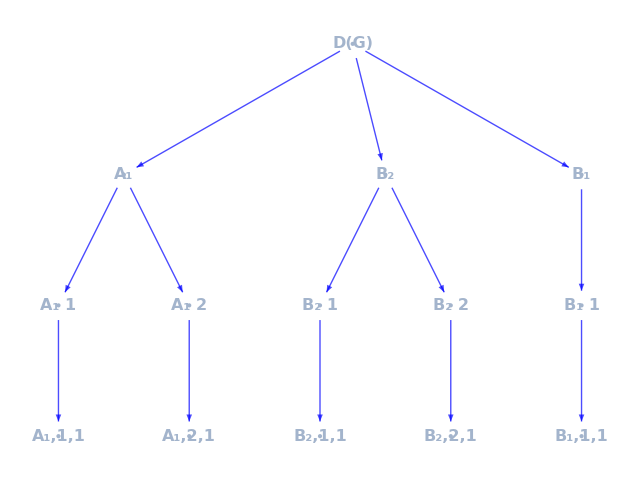

{{A_1,1,1
A_1,2,1},{B_2,1,1
B_2,2,1},{B_1,1,1}}

{{(1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)},{(1 | -1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)},{(0 | 0 | 0 | 1 | 0)}}

```mathematica
graph=Flatten@Table[{"D(G)"->irepNm[[μ]],Table[{irepNm[[μ]]->ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t,Table[ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t->irepNm[[μ]],t,m,{m,1,irepSize[[μ]]}]},{t,1,frequencies[[μ]]}]},{μ,presentIrreps}];
ef1[el_,___]:={Arrowheads[0.01],Arrow[el,0.09]};
LayeredGraphPlot[graph,GraphLayout->"LayeredEmbedding",VertexLabels->Table[v->Placed[Style[v,Bold,16],Center],{v,VertexList@graph}],VertexShapeFunction->None,ImageSize->640,EdgeStyle->Blue,EdgeShapeFunction->ef1,PlotRangePadding->Scaled[.1]]

(MatrixForm/@#)&/@Table[Table[Column@Table[irepNm[[μ]],t,m,{t,1,frequencies[[μ]]}],{m,1,irepSize[[μ]]}],{μ,presentIrreps}]
(MatrixForm/@#)&/@SAB
```

We can find out what the general symmetry obeying hamiltonian has to look like by solving the system of equations D(g) H = H D(g) ∀g ϵ G. The hamiltonian must commute with the symmetry operators!

```mathematica
H=Table[Subscript[mat, i,j],{i,Length@representation[[1]]},{j,Length@representation[[1]]}];
Do[H=FullSimplify[H/.Flatten[Solve[H.representation[[#]]==representation[[#]].H]&/@Range@Length@G]],4];
MatrixForm@H
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

(mat_(1,1) | mat_(1,2) | mat_(1,3) | 0 | mat_(1,5)
mat_(1,2) | mat_(1,1) | -mat_(1,3) | 0 | mat_(1,5)
mat_(3,1) | -mat_(3,1) | mat_(3,3) | 0 | 0
0 | 0 | 0 | mat_(4,4) | 0
mat_(5,1) | mat_(5,1) | 0 | 0 | mat_(5,5))

```mathematica
(H=H/.{Subscript[mat, 1,1]->Subscript[ϵ, s],Subscript[mat, 1,2]->Subscript[t, s],Subscript[mat, 2,1]->Subscript[t, s],Subscript[mat, 1,3]->Subscript[t, Subscript[sp, x]],Subscript[mat, 3,1]->SuperStar[Subscript[t, Subscript[sp, x]]],Subscript[mat, 1,5]->Subscript[t, Subscript[sp, z]],Subscript[mat, 5,1]->SuperStar[Subscript[t, Subscript[sp, z]]],Subscript[mat, i_,i_]->Subscript[ϵ, Subscript[p, i]]})//MatrixForm
```

(ϵ_s | t_s | t_sp_x | 0 | t_sp_z
t_s | ϵ_s | -t_sp_x | 0 | t_sp_z
(t_sp_x)^* | -(t_sp_x)^* | ϵ_p_3 | 0 | 0
0 | 0 | 0 | ϵ_p_4 | 0
(t_sp_z)^* | (t_sp_z)^* | 0 | 0 | ϵ_p_5)

We see that the hamiltonian has 7 free parameters. The symmetry group C2v allows ϵ_p_ito be different but they are actually the same. So actually there are 7 - 2 = 5 free parameters.

```mathematica
(H=H/.{Subscript[ϵ, Subscript[p, i_]]->Subscript[ϵ, p]})//MatrixForm
```

(ϵ_s | t_s | t_sp_x | 0 | t_sp_z
t_s | ϵ_s | -t_sp_x | 0 | t_sp_z
(t_sp_x)^* | -(t_sp_x)^* | ϵ_p | 0 | 0
0 | 0 | 0 | ϵ_p | 0
(t_sp_z)^* | (t_sp_z)^* | 0 | 0 | ϵ_p)

We now reduce the hamiltonian into symmetry invariant subspaces given by the decomposition of our atomic orbital representaion into irreps. In this step I have normalized the

```mathematica
Grid[Table[{"H ↓ "<>ToString[irepNm[[presentIrreps[[μ]]]],StandardForm],MatrixForm@FullSimplify[operatorReduce[H,Flatten[Table[SAB[[μ,All,t]]/Norm@SAB[[μ,All,t]],{t,frequencies[[presentIrreps[[μ]]]]}],1]]]},{μ,1,Length@presentIrreps}],Frame->All]
```

H ↓ A_1 | (t_s+ϵ_s | √2 t_sp_z
√2 (t_sp_z)^* | ϵ_p)
H ↓ B_2 | (-t_s+ϵ_s | √2 t_sp_x
√2 (t_sp_x)^* | ϵ_p)
H ↓ B_1 | (ϵ_p)

This reduction has greatly simplified the eigenproblem of the hamiltonian. The eigenproblem is solved with the following eigenvalues

```mathematica
Grid[({#[[1]],FullSimplify@Eigensystem[#[[2]]]})&/@Table[{irepNm[[presentIrreps[[μ]]]],operatorReduce[H,Flatten[Table[SAB[[μ,All,t]],{t,frequencies[[presentIrreps[[μ]]]]}],1]]},{μ,1,Length@presentIrreps}],Frame->All]
```

A_1 | {{1/2 (t_s+ϵ_p+ϵ_s-√((t_s-ϵ_p+ϵ_s)^2+8 t_sp_z (t_sp_z)^*)),1/2 (t_s+ϵ_p+ϵ_s+√((t_s-ϵ_p+ϵ_s)^2+8 t_sp_z (t_sp_z)^*))},{{(t_s-ϵ_p+ϵ_s-√((t_s-ϵ_p+ϵ_s)^2+8 t_sp_z (t_sp_z)^*))/(4 (t_sp_z)^*),1},{(t_s-ϵ_p+ϵ_s+√((t_s-ϵ_p+ϵ_s)^2+8 t_sp_z (t_sp_z)^*))/(4 (t_sp_z)^*),1}}}
B_2 | {{1/2 (-t_s+ϵ_p+ϵ_s-√((t_s+ϵ_p-ϵ_s)^2+8 t_sp_x (t_sp_x)^*)),1/2 (-t_s+ϵ_p+ϵ_s+√((t_s+ϵ_p-ϵ_s)^2+8 t_sp_x (t_sp_x)^*))},{{-(t_s+ϵ_p-ϵ_s+√((t_s+ϵ_p-ϵ_s)^2+8 t_sp_x (t_sp_x)^*))/(4 (t_sp_x)^*),1},{(-t_s-ϵ_p+ϵ_s+√((t_s+ϵ_p-ϵ_s)^2+8 t_sp_x (t_sp_x)^*))/(4 (t_sp_x)^*),1}}}
B_1 | {{ϵ_p},{{1}}}

We see that the hamiltonian is succesfully reduced.

Here I will attempt to draw these orbitals.

```mathematica
sOrbital[x_,y_,z_]:=Exp[-Sqrt[x^2+y^2+z^2]];
pxOrbital[x_,y_,z_]:=√3 Exp[-Sqrt[x^2+y^2+z^2]]x;
pyOrbital[x_,y_,z_]:=√3 Exp[-Sqrt[x^2+y^2+z^2]]y;
pzOrbital[x_,y_,z_]:=√3 Exp[-Sqrt[x^2+y^2+z^2]]z;
```

```mathematica
AtomicOrbitals=Join[sOrbital[x-#[[1]],y-#[[2]],z-#[[3]]]&/@atompositions[[1;;2]],({pxOrbital[x-#[[1]],y-#[[2]],z-#[[3]]],
pyOrbital[x-#[[1]],y-#[[2]],z-#[[3]]],
pzOrbital[x-#[[1]],y-#[[2]],z-#[[3]]]})&@atompositions[[3]]];
```

```mathematica
Grid[{{"Atomic orbitals",SpanFromLeft},Show[ContourPlot3D[#,{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,Contours->{-0.5,0.5},ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{{PointSize[0.02],Point[#]}&/@atompositions[[1;;2]],{PointSize[0.05],Point[#]}&@atompositions[[3]]}]]&/@AtomicOrbitals},Frame->All]
```

Atomic orbitals |  |  |  | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Grid[Table[Table[Show[Table[ContourPlot3D[#,{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,Contours->({-0.5,0.5}[[level]]),ContourStyle->Directive[{Blue,Red}[[level]],Opacity[0.4],Specularity[White,30]],AspectRatio->1,PlotLabel->"Molecular orbital"<>ToString[irepNm[[presentIrreps[[μ]]]],t,1,StandardForm]],{level,{1,2}}],
Graphics3D[{{PointSize[0.02],Point[#]}&/@atompositions[[1;;2]],{PointSize[0.05],Point[#]}&@atompositions[[3]]}]]&@(SAB[[μ,All,t]].AtomicOrbitals),{t,frequencies[[presentIrreps[[μ]]]]}],{μ,1,Length@presentIrreps}],Frame->All]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- |

# Benzene molecule

Here, I will construct the molecular orbitals of benzene by combining six p_z orbitals on each carbon atom.

```mathematica
G=GTInstallGroup[D6h]; (* The symmetry group of benzene is D6h *)
atoms=Join[(Style[Subscript[C, #],Bold,16,Blue])&/@Range[6]] (* benzene consists of 6 carbon atoms *)
```

The standard representation has changed to O(3)

{C_1,C_2,C_3,C_4,C_5,C_6}

Group D6h acts on this vector space by permuting some orbitals and by sometimes flipping them upside down. This is encoded with a tensor product of  the permutation representation, permutationRepresentation2, and  the usual vector representation of O(3) acting on the orbital p_z. The action on this orbital is the same as the action onto the basis vector e_z. 
atompositions contains the positions of carbon atoms in this molecule. Because I know for a fact one atom is found at {1, 0, 0}, I can get other atoms’ positions by acting with G on them. Point {1,0,0} is right on one of the symmetry axes of G in GTPack.

```mathematica
positions=DeleteDuplicates[(GTGetMatrix[#].{1,0,0})&/@G]//Sort;
permutationRepresentation1=Table[(Position[positions,GTGetMatrix[g].#][[1]][[1]])&/@positions,{g,G}];
permutationRepresentation2=Table[SparseArray[Table[{permutationRepresentation1[[j]][[i]],i}->1,{i,Length@atoms}]],{j,Length@G}];
Grid[{(Style[#,Bold,18])&/@G,(MatrixPlot[#,FrameTicks->None])&/@permutationRepresentation2}];
dpv=GTGetMatrix/@G;
MatrixPlot/@(representation=KroneckerProduct[permutationRepresentation2[[#]],{dpv[[#]][[3,3]]}]&/@Range@Length@G);
```

```mathematica
decompose[repchars_]:=FullSimplify@(FullSimplify@(1/(Length@G)Conjugate@irepCh).repchars); (* Vraća vektor frekvencija ira u razlaganju reprezentacija sa karakterima repchars_ *)
decomposeUserFriendly[repchars_]:=ToString[StringReplace[ToString[decompose[repchars].irepNm,FormatType->StandardForm],{"+"->"⊕"}],FormatType->StandardForm];
GroupProjectionOperator[μ_,representation_]:=irepSize[[μ]]/(Length@G)(Conjugate@irepCh[[μ]]).representation;
(* Grupni projektor na ukupni potprostor čiji se vektori transformišu po iri μ, korisno je ali ne daje stvari u skladu sa metodom grupnih projektora od Džambe i svi vektori iz SAB za datu iru se pomešaju. *)

GroupProjectionOperatorDetailed[μ_,representation_]:=FullSimplify[irepSize[[μ]]/(Length@G)Partition[Sum[KroneckerProduct[irreps[[μ,k,1]],representation[[k]]],{k,Length@G}],Length@representation[[1]]]];(* Vraća listu grupnih projektora {Subscript[(P^(μ)), 11],Subscript[(P^(μ)), 12],...,(P^(μ))_(1|μ|),} Prva matrica u nizu je projektor dok su druge one push matrice kojima treba gurnuti sliku prvog projektora. *)
ShomyProjection[μ_,representation_]:=Module[{out},out=irepSize[[μ]]/(Length@G)Partition[FullSimplify@Sum[KroneckerProduct[irreps[[μ,k,1]],representation[[k]]],{k,Length@G}],Length@representation[[1]]];
FullSimplify@((ConjugateTranspose[#].out[[1]].#)&/@out)](* Lično smatram da je ovo jako pametno parče koda koje sam sam smislio xD *)
```

```mathematica
groupData=GTGetIreps[G,GOIrepNotation->"Mulliken",GOVerbose->False];
irreps=groupData[[2]][[2]]; (* Tablice ira *)
irepCh=FullSimplify@(Tr/@#)&/@irreps; (* karakteri ira nad elementima grupe *)
irepNm=groupData[[1]][[3]]; (* Imena ira *)
nirreps=GTNumberOfIreps[G]; (* Broj ira *)
irepSize=(Length@irreps[[#,1]])&/@Range@nirreps;
```

The given group has 12 non-equivalent irreducible representations.

```mathematica
frequencies=decompose[Tr/@representation];
presentIrreps=Table[If[frequencies[[i]]≠0,i,Nothing],{i,nirreps}];
decomposeUserFriendly[Tr/@representation]
```

A_(2u)⊕B_(2g)⊕E_(1g)⊕E_(2u)

Relevantna stvar za suženje operatora na invarijantni potprostor. Ukoliko potprostor nije invarijantan, funkcija vraća nula-matricu.

```mathematica
operatorReduce[operator_,basis_]:=Module[{image=(operator.#)&/@basis,out={}},Transpose@Table[Flatten[Table[a[j],{j,Length@basis}]/.Solve[
Sum[a[k]basis[[k]],{k,Length@basis}]==image[[i]],Table[a[k],{k,1,Length@basis}]
],2],
{i,Length@basis}]];
DirectSum[a_List?MatrixQ,b_List?MatrixQ]:=ArrayFlatten[{{a,0},{0,b}}](* Ovaj kod je maznut sa interneta *)
```

Group projection operators techique.

```mathematica
projs=ShomyProjection[#,representation]&/@presentIrreps;(* Ova komanda vraća spisak projektora Subscript[(P^(μ)), m m] koji se potom row-reduceuju itd *)
SAB=Map[RowReduce,projs,{2}];
SAB=Map[(If[#==0*#,Nothing,#])&,SAB,3];
(MatrixForm/@#)&/@SAB;
```

Symmetry adapted basis is organized as follows:

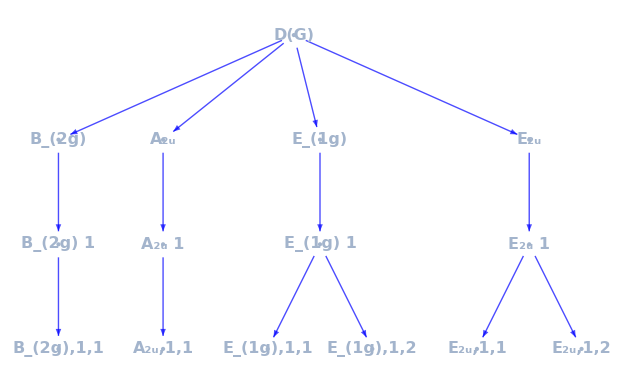

{{B_(2g),1,1},{A_(2u),1,1},{E_(1g),1,1,E_(1g),1,2},{E_(2u),1,1,E_(2u),1,2}}

{{(1 | -1 | -1 | 1 | 1 | -1)},{(1 | 1 | 1 | 1 | 1 | 1)},{(1 | 1/2+(ⅈ √3)/2 | 1/2-(ⅈ √3)/2 | -1/2+(ⅈ √3)/2 | -1/2-(ⅈ √3)/2 | -1),(1 | 1/2-(ⅈ √3)/2 | 1/2+(ⅈ √3)/2 | -1/2-(ⅈ √3)/2 | -1/2+(ⅈ √3)/2 | -1)},{(1 | -1/2-(ⅈ √3)/2 | -1/2+(ⅈ √3)/2 | -1/2+(ⅈ √3)/2 | -1/2-(ⅈ √3)/2 | 1),(1 | -1/2+(ⅈ √3)/2 | -1/2-(ⅈ √3)/2 | -1/2-(ⅈ √3)/2 | -1/2+(ⅈ √3)/2 | 1)}}

```mathematica
graph=Flatten@Table[{"D(G)"->irepNm[[μ]],Table[{irepNm[[μ]]->ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t,Table[ToString[irepNm[[μ]],FormatType->StandardForm]<>" "<>ToString@t->irepNm[[μ]],t,m,{m,1,irepSize[[μ]]}]},{t,1,frequencies[[μ]]}]},{μ,presentIrreps}];
ef1[el_,___]:={Arrowheads[0.01],Arrow[el,0.09]};
LayeredGraphPlot[graph,GraphLayout->"LayeredEmbedding",VertexLabels->Table[v->Placed[Style[v,Bold,16],Center],{v,VertexList@graph}],VertexShapeFunction->None,ImageSize->640,EdgeStyle->Blue,EdgeShapeFunction->ef1,PlotRangePadding->Scaled[.1]]
decomposeUserFriendly[Tr/@representation];
(MatrixForm/@#)&/@Table[Table[Column@Table[irepNm[[μ]],t,m,{t,1,frequencies[[μ]]}],{m,1,irepSize[[μ]]}],{μ,presentIrreps}]
(MatrixForm/@#)&/@Expand@SAB
```

```mathematica
Clear[t]
```

```mathematica
H=Table[Subscript[mat, i,j],{i,Length@representation[[1]]},{j,Length@representation[[1]]}];
Do[H=FullSimplify[H/.Flatten[Solve[H.representation[[#]]==representation[[#]].H]&/@Range@Length@G]],4];
MatrixForm@H
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

(mat_(1,1) | mat_(1,2) | mat_(1,2) | mat_(1,4) | mat_(1,4) | mat_(1,6)
mat_(1,2) | mat_(1,1) | mat_(1,4) | mat_(1,2) | mat_(1,6) | mat_(1,4)
mat_(1,2) | mat_(1,4) | mat_(1,1) | mat_(1,6) | mat_(1,2) | mat_(1,4)
mat_(1,4) | mat_(1,2) | mat_(1,6) | mat_(1,1) | mat_(1,4) | mat_(1,2)
mat_(1,4) | mat_(1,6) | mat_(1,2) | mat_(1,4) | mat_(1,1) | mat_(1,2)
mat_(1,6) | mat_(1,4) | mat_(1,4) | mat_(1,2) | mat_(1,2) | mat_(1,1))

```mathematica
(H=H/.{Subscript[mat, i_,i_]->Subscript[ϵ, 0],Subscript[mat, 1,2]->Subscript[t, 1],Subscript[mat, 1,4]->Subscript[t, 2],Subscript[mat, 1,6]->Subscript[t, 3]})//MatrixForm
```

(ϵ_0 | t_1 | t_1 | t_2 | t_2 | t_3
t_1 | ϵ_0 | t_2 | t_1 | t_3 | t_2
t_1 | t_2 | ϵ_0 | t_3 | t_1 | t_2
t_2 | t_1 | t_3 | ϵ_0 | t_2 | t_1
t_2 | t_3 | t_1 | t_2 | ϵ_0 | t_1
t_3 | t_2 | t_2 | t_1 | t_1 | ϵ_0)

```mathematica
(H.representation[[#]]==representation[[#]].H)&/@Range@Length@G
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
MatrixForm@H
```

(ϵ_0 | t_1 | t_1 | t_2 | t_2 | t_3
t_1 | ϵ_0 | t_2 | t_1 | t_3 | t_2
t_1 | t_2 | ϵ_0 | t_3 | t_1 | t_2
t_2 | t_1 | t_3 | ϵ_0 | t_2 | t_1
t_2 | t_3 | t_1 | t_2 | ϵ_0 | t_1
t_3 | t_2 | t_2 | t_1 | t_1 | ϵ_0)

We now reduce the hamiltonian into symmetry invariant subspaces given by the decomposition of our atomic orbital representaion into irreps. In this step I have normalized the

```mathematica
Grid[Table[{"H ↓ "<>ToString[irepNm[[presentIrreps[[μ]]]],StandardForm],MatrixForm@FullSimplify[operatorReduce[H,Flatten[Table[SAB[[μ,All,t]]/Norm@SAB[[μ,All,t]],{t,frequencies[[presentIrreps[[μ]]]]}],1]]]},{μ,1,Length@presentIrreps}],Frame->All]
```

H ↓ B_(2g) | (-2 t_1+2 t_2-t_3+ϵ_0)
H ↓ A_(2u) | (2 t_1+2 t_2+t_3+ϵ_0)
H ↓ E_(1g) | (t_1-t_2-t_3+ϵ_0 | 0
0 | t_1-t_2-t_3+ϵ_0)
H ↓ E_(2u) | (-t_1-t_2+t_3+ϵ_0 | 0
0 | -t_1-t_2+t_3+ϵ_0)

This reduction has greatly simplified the eigenproblem of the hamiltonian. The eigenproblem is solved with the following eigenvalues and eigenvectors

```mathematica
Grid[({#[[1]],FullSimplify@Eigensystem[#[[2]]]})&/@Table[{irepNm[[presentIrreps[[μ]]]],operatorReduce[H,Flatten[Table[SAB[[μ,All,t]],{t,frequencies[[presentIrreps[[μ]]]]}],1]]},{μ,1,Length@presentIrreps}],Frame->All]
```

B_(2g) | {{-2 t_1+2 t_2-t_3+ϵ_0},{{1}}}
A_(2u) | {{2 t_1+2 t_2+t_3+ϵ_0},{{1}}}
E_(1g) | {{t_1-t_2-t_3+ϵ_0,t_1-t_2-t_3+ϵ_0},{{0,1},{1,0}}}
E_(2u) | {{-t_1-t_2+t_3+ϵ_0,-t_1-t_2+t_3+ϵ_0},{{0,1},{1,0}}}

Here I will attempt to draw the 6 molecular orbitals.

```mathematica
pzOrbital[x_,y_,z_]:=√3 Exp[-Sqrt[x^2+y^2+z^2]]z;
```

```mathematica
AtomicOrbitals=pzOrbital[x-#[[1]],y-#[[2]],z-#[[3]]]&/@positions;
```

```mathematica
Grid[{{"Atomic orbitals",SpanFromLeft},Show[ContourPlot3D[#,{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,Contours->{-0.5,0.5},ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&/@AtomicOrbitals},Frame->All]
```

Atomic orbitals |  |  |  |  | 
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Grid[{{"Molecular orbital "<>ToString[irepNm[[presentIrreps[[1]]]],1,1,StandardForm]},{Show[ContourPlot3D[{#==-0.09,#==0.09},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}}],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[1,All,1]].AtomicOrbitals)}},Frame->All]
```

Molecular orbital B_(2g)
-Graphics3D-

```mathematica
Grid[{{"Molecular orbital "<>ToString[irepNm[[presentIrreps[[2]]]],1,1,StandardForm]},{Show[ContourPlot3D[{#==2.25,#==-2.25},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[2,1,1]].AtomicOrbitals)}},Frame->All]
```

Molecular orbital A_(2u)
-Graphics3D-

```mathematica
Grid[{{"Real and imaginary parts of "<>ToString[irepNm[[presentIrreps[[3]]]],1,1,StandardForm],SpanFromLeft},{Show[ContourPlot3D[{Re@#==-0.5,Re@#==0.5},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[3,1,1]].AtomicOrbitals),Show[ContourPlot3D[{Im@#==-0.5,Im@#==0.5},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[3,1,1]].AtomicOrbitals)}},Frame->All]
```

Real and imaginary parts of E_(1g) | 
-Graphics3D- | -Graphics3D-

```mathematica
Grid[{{"Real and imaginary parts of "<>ToString[irepNm[[presentIrreps[[3]]]],1,2,StandardForm],SpanFromLeft},{Show[ContourPlot3D[{Re@#==-0.5,Re@#==0.5},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[3,2,1]].AtomicOrbitals),Show[ContourPlot3D[{Im@#==-0.5,Im@#==0.5},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[3,2,1]].AtomicOrbitals)}},Frame->All]
```

Real and imaginary parts of E_(1g) | 
-Graphics3D- | -Graphics3D-

```mathematica
Grid[{{"Real and imaginary parts of "<>ToString[irepNm[[presentIrreps[[4]]]],1,1,StandardForm],SpanFromLeft},{Show[ContourPlot3D[{Re@#==-0.17,Re@#==0.17},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[4,1,1]].AtomicOrbitals),Show[ContourPlot3D[{Im@#==-0.17,Im@#==0.17},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[4,1,1]].AtomicOrbitals)}},Frame->All]
```

Real and imaginary parts of E_(2u) | 
-Graphics3D- | -Graphics3D-

```mathematica
Grid[{{"Real and imaginary parts of "<>ToString[irepNm[[presentIrreps[[4]]]],1,2,StandardForm],SpanFromLeft},{Show[ContourPlot3D[{Re@#==-0.17,Re@#==0.17},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[4,2,1]].AtomicOrbitals),Show[ContourPlot3D[{Im@#==-0.17,Im@#==0.17},{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->5,Mesh->None,ContourStyle->{{Opacity[0.4],Specularity[White,30],Blue},{Opacity[0.4],Specularity[White,30],Red}},AspectRatio->1],
Graphics3D[{PointSize[0.05],Point[#]}&/@positions]]&@(SAB[[4,2,1]].AtomicOrbitals)}},Frame->All]
```

Real and imaginary parts of E_(2u) | 
-Graphics3D- | -Graphics3D-